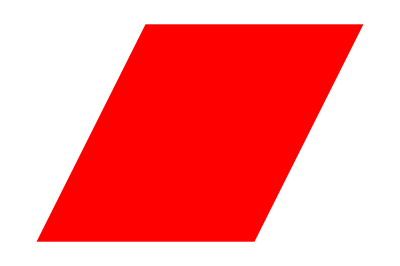

```mathematica
Graphics[{Red, Parallelogram[{0, 0}, {{1/2, 1}, {1, 0}}]}]
```

```mathematica
a = {1, 0, 0};
b = 1/2{1, √3, 0};
origin = {0, 0, 0};

crossDiagram =Graphics3D[{
(*Opacity[.5], (* Makes area of Parallelogram transparent *)
Yellow,
Polygon[{origin, a, a+b,  b}], (* Forms Parallelogram made by a and b*)
Opacity[1], *)
GrayLevel[0],  
Arrow[{origin, a}], (* Vector a *)
Text[Style[Pane["a", ImageMargins-> 1], 20, Bold], (1/2)a-{0, .1, 0}],
Arrow[{origin, b}], (* Vector b *)
Text[Style[Pane["b", ImageMargins-> 1], 20, Bold], (1/2)b-{.2, 0, 0}],
Arrow[{origin, Cross[a, b]}], (* Vector a × b *)
Text[Style[Pane["a × b", ImageMargins-> 1], 20, Bold], (1/2)Cross[a, b] + {0, .2, 0}]
}]; 
Show[crossDiagram, Boxed -> False]
```

-Graphics3D-

```mathematica
a = {1, 0, 0};
b = 1/2{1, √3, 0};
c = 1/2{1, 1, √3};
origin = {0, 0, 0};

crossDiagram =Graphics3D[{
Opacity[.05], (* Makes area of Parallelogram transparent *)
GrayLevel[0.75],
Parallelepiped[origin, {a, b, c}], (* Forms Parallelogram made by a and b*)
Opacity[1],
GrayLevel[0], 
Arrow[{origin, a}], (* vector a *)
Text[Style[Pane["a", ImageMargins-> 1], 20, Bold], (1/2)a-{0, .1, 0}], 
Arrow[{origin, b}], (* Vector b *)
Text[Style[Pane["b", ImageMargins-> 1], 20, Bold], (1/2)b-{.2, 0, 0}],
Arrow[{origin, c}], (* Vector a × b *)
Text[Style[Pane["c", ImageMargins-> 1], 20, Bold], (1/2)Cross[a, b] + {0, .2, 0}]
}]; 
Show[crossDiagram, Boxed -> False]
```

-Graphics3D-